```mathematica
lambda = 1.064 * 10^-6 (*in nm*)
```

1.064×10^-6

```mathematica
nO = 1.54422
nE = 1.55332
```

1.54422

1.55332

```mathematica
lambdaO = lambda/nO
lambdaE = lambda / nE
```

6.89021×10^-7

6.84984×10^-7

```mathematica
kE = 2Pi/lambdaE
kO = 2Pi /lambdaO
```

9.17274×10^6

9.119×10^6

```mathematica
r = .5 * 10^-5
z = 1  * 10^-5


(* r serves as the radius, and z serves as the height of the cylinder in nm*)
```

5.×10^-6

1/100000

```mathematica
V = Pi * z * r^2
rho = 2660 (*kg per m^3*)
m = V * rho (* in kg *)
(*moment of intertia for cylinder*)
Iz = .5 *m *r^2
```

7.85398×10^-16

2660

2.08916×10^-12

2.61145×10^-23

```mathematica
eta= z(kE - kO)
```

0.537378

```mathematica
h = 6.62607004×10^-34 (*plancks and reduced plancks constant*)
hbar = h / (2 * Pi)

c = 299792458 (*light in m/s*)
```

6.62607×10^-34

1.05457×10^-34

299792458

```mathematica
EnergyP = h * c / lambda (*the energy of one photon emitted by the laser*)
```

1.86696×10^-19

```mathematica
P = 10 * 10^-3 (*power of the laser*)
```

1/100

```mathematica
NumPhot = P / EnergyP (* the number of photons per second*)
```

5.3563×10^16

```mathematica
(*arbitrary for Jones Matrix*)
theta = Pi/4
phi = 0
```

π/4

0

0

```mathematica
(*Here we set the Jones vector for an arbitrary medium, and we set the light vector that is under our control*)
```

```mathematica
InJones = {{(Cos [theta])^2 + E^(I * eta)((Sin  [theta])^2), (1 - (E ^ (I * eta))) (E ^( -I * phi))(Cos [theta])(Sin [theta])}, {(1 - E ^ (I * eta)) (E ^( I * phi)(Cos [theta])(Sin [theta])), ((Sin [theta])^2 )+ E^(I * eta)((Cos  [theta])^2)}}
```

{{0.929527+0.255943 ⅈ,0.070473-0.255943 ⅈ},{0.070473-0.255943 ⅈ,0.929527+0.255943 ⅈ}}

```mathematica
InJones // MatrixForm
```

(0.929527+0.255943 ⅈ | 0.070473-0.255943 ⅈ
0.070473-0.255943 ⅈ | 0.929527+0.255943 ⅈ)

```mathematica
Jones = (E ^ (-I * eta /2)) * InJones
Jones // MatrixForm
Light = 1/Sqrt[2]{1,I}
```

{{0.96412-2.77556×10^-17 ⅈ,0.-0.265468 ⅈ},{0.-0.265468 ⅈ,0.96412-2.77556×10^-17 ⅈ}}

(0.96412-2.77556×10^-17 ⅈ | 0.-0.265468 ⅈ
0.-0.265468 ⅈ | 0.96412-2.77556×10^-17 ⅈ)

{1/(√2),ⅈ/(√2)}

```mathematica
Light // MatrixForm
```

(1/(√2)
ⅈ/(√2))

```mathematica
Outputlight=Jones.Light
```

{0.86945-1.96262×10^-17 ⅈ,1.96262×10^-17+0.494022 ⅈ}

```mathematica
Outputlight // MatrixForm
```

(0.96412-0.265468 ⅈ
0.+0. ⅈ)

```mathematica
LPol = 1/Sqrt [2]{1,I}
RPol = 1/Sqrt [2]{1,-I}
```

{1/(√2),ⅈ/(√2)}

{1/(√2),-ⅈ/(√2)}

```mathematica
(*puts output light in the basis of right and left circular polarized light*)
OutLPol = Projection[Outputlight,LPol] //MatrixForm
OutRPol = Projection[Outputlight, RPol] // MatrixForm


InputRpol = Projection[Light, RPol] // MatrixForm
InputLpol = Projection[Light, LPol] // MatrixForm
```

(0.681736-1.96262×10^-17 ⅈ
1.96262×10^-17+0.681736 ⅈ)

(0.187714+0. ⅈ
0.-0.187714 ⅈ)

(0
0)

(1/(√2)
ⅈ/(√2))

```mathematica
(* we can solve for the coefficients of our cirular basis, alpha (RPOL) and beta (LPOL) using a system of equations*)
alphaOut = Sqrt[2]/2(Outputlight[[1]] + (Outputlight[[1]]/I))
alphaIn =  Sqrt[2]/2(Light[[1]] + (Light[[2]]/I))
betaOut = Sqrt[2]/2(Outputlight[[1]] - (Outputlight[[2]]/I))
betaIn = Sqrt[2]/2(Light[[1]] - (Light[[2]]/I))
```

0.614794-0.614794 ⅈ

1

0.265468+0. ⅈ

0

```mathematica
L0 = (hbar*(Abs[betaIn]^2)-hbar*(Abs[alphaIn])^2) (*avg spin L for incoming photons*)
L1 = (hbar*(Abs[betaOut]^2) - hbar*(Abs[alphaOut])^2) (*avg spin L for outgoing phtons *)
```

-1.05457×10^-34

-7.22877×10^-35

```mathematica
(*Delta L gives us the average change in spin L for a single photon*)
```

```mathematica
DeltaL = L1 - L0

onesecDeltaL = NumPhot * DeltaL
```

3.31695×10^-35

1.77666×10^-18

```mathematica
angacc =onesecDeltaL / Iz (*this is the angular acceleration of the cylinder due to the laser in m/sec^2*)
```

68033.4

```mathematica
(*now we are going to solve the differential equation for the acceleration of the gas in the vacuum chamber*)

sigma = 1 (* tangential momentum transfer coefficient*)
pressure = 1 * 10^-5 (*pascals*)
```

1

1/100000

```mathematica
R = 8.3145 (*molar gas constant*)
T= 293 (*room temp in Kelvin*)
Mm = 2.1 (*predominantly H2 remains at lower pressures. At higher pressures N2 dominates*)
cbar= Sqrt[3*R*T/Mm](*mean molecular velocity*)
```

```mathematica
(* look into whether coefficients need to be squared. check why 10^-15 instead of 10^-5*)
```

```mathematica
eqn = {w'[t]== -w[t]*sigma*(10/Pi)*(1/(rho*r))*(pressure/cbar)+angacc,w[0]== 0}
```

{w'[t]==68033.4-0.0000405691 w[t],w[0]==0}

```mathematica
sol=DSolve[eqn,w[t],t]
```

{{w[t]→1.67698×10^9 ⅇ^(-0.0000405691 t) (-1.+1. ⅇ^(0.0000405691 t))}}

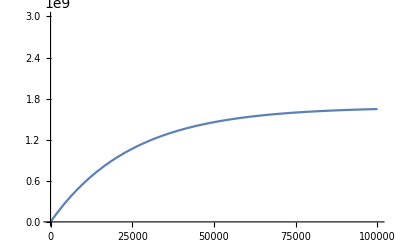

```mathematica
Plot[w[t]/.sol,{t,0,1*10^5},PlotRange->{0,3*10^9}]
```

```mathematica
(*t is in seconds*)
```

Projection::prnv: The first or second argument or both are not vectors, or they are not vectors of equal length.

Set::wrsym: Symbol Left is Protected.